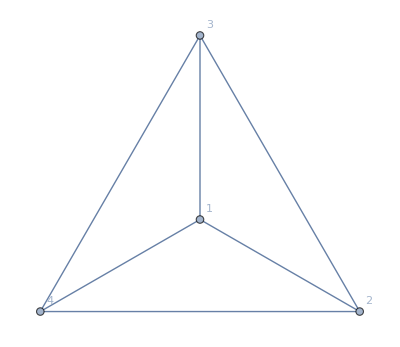

```mathematica
g=WheelGraph[4,VertexLabels->"Name"]
```

```mathematica
gf=Expand[CalculateInOutFormulaMany[g,{{2,3,4},{1}}]]
```

-6 B1+2 A2 B1-A2x3 B1+A2x3x4 B1-A2x4 B1+2 A3 B1-A3x4 B1+2 A4 B1

```mathematica
Collect[gf,B1]
```

(-6+2 A2-A2x3+A2x3x4-A2x4+2 A3-A3x4+2 A4) B1

```mathematica
gf1=Collect[gf,B1]/B1
```

-6+2 A2-A2x3+A2x3x4-A2x4+2 A3-A3x4+2 A4

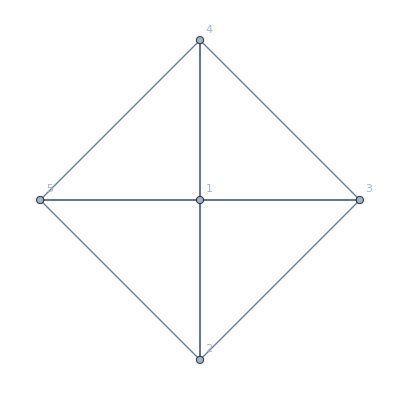

```mathematica
h=EdgeAdd[g,{5<->2,5<->3,5<->4,5<->1}]
```

```mathematica
hf=Expand[CalculateInOutFormulaMany[h,{{2,3,4},{1},{5}}]]
```

24 C5-6 A2 C5+2 A2x3 C5-A2x3x4 C5+2 A2x4 C5-6 A3 C5+2 A3x4 C5-6 A4 C5-24 B1 C5+6 A2 B1 C5-2 A2x3 B1 C5+A2x3x4 B1 C5-2 A2x4 B1 C5+6 A3 B1 C5-2 A3x4 B1 C5+6 A4 B1 C5

```mathematica
hf6=Collect[hf,C5]
```

(24-6 A2+2 A2x3-A2x3x4+2 A2x4-6 A3+2 A3x4-6 A4-24 B1+6 A2 B1-2 A2x3 B1+A2x3x4 B1-2 A2x4 B1+6 A3 B1-2 A3x4 B1+6 A4 B1) C5

```mathematica
Collect[hf6/C5,B1]
```

18-4 A2+A2x3+A2x4-4 A3+A3x4-4 A4+(-24+6 A2-2 A2x3+A2x3x4-2 A2x4+6 A3-2 A3x4+6 A4) B1

```mathematica
MyForm[f_]:=Block[{var},
Table[
var=ListofVars[f[[l]]];
If[var≠{},var=First[var]];
f[[l]]*If[var==={},4,4-SymbolLevel[var]]
,{l,Length[f]}
]
]
```

```mathematica
MyForm2[f_]:=Block[{var},
Table[
var=ListofVars[f[[l]]];
If[var≠{},var=First[var]];
f[[l]]/If[var==={},3,3-SymbolLevel[var]]
,{l,Length[f]}
]
]
```

```mathematica
MyForm[gf1]//Total
```

-24+6 A2-2 A2x3+A2x3x4-2 A2x4+6 A3-2 A3x4+6 A4

```mathematica
(MyForm2[18-4 A2+A2x3+A2x4-4 A3+A3x4-4 A4]//Total)
```

6-2 A2+A2x3+A2x4-2 A3+A3x4-2 A4

```mathematica
-gf1
```

6-2 A2+A2x3-A2x3x4+A2x4-2 A3+A3x4-2 A4

```mathematica
gf1+(MyForm2[Coefficient[Collect[hf6/C5,B1],B1]]//Total)//Simplify
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Coefficient[Collect[hf6/C5,B1],B1]
```

-24+6 A2-2 A2x3+A2x3x4-2 A2x4+6 A3-2 A3x4+6 A4

```mathematica
Collect[hf6,B1]
```

(24-6 A2+2 A2x3-A2x3x4+2 A2x4-6 A3+2 A3x4-6 A4) C5+(-24+6 A2-2 A2x3+A2x3x4-2 A2x4+6 A3-2 A3x4+6 A4) B1 C5

```mathematica
Coefficient[Collect[hf6,B1],B1]/C5
```

-24+6 A2-2 A2x3+A2x3x4-2 A2x4+6 A3-2 A3x4+6 A4

```mathematica
MyForm[Coefficient[Collect[hf6,B1],B1]/C5]
```

{-96,18 A2,-4 A2x3,A2x3x4,-4 A2x4,18 A3,-4 A3x4,18 A4}